```mathematica
data2={{1048,130},{1040,131},{1035,132},{1025,134},{1020,135},{1015,136},{1011,137},{1006,138},{1000,139},{995,140},{990,141},{985,142},{980,143},{970,144},{961,145},{951,146},{940,148},{931,150},{920,151},{910,152},{900,153},{891,154},{880,157},{870,159},{860,161},{850,163},{840,165},{830,167},{820,169},{810,171},{800,174},{790,177},{780,180},{771,183},{760,186},{750,189},{740,192},{730,195},{720,199},{710,202},{700,205},{690,208},{680,211},{670,215},{660,220},{650,225},{640,230},{630,235},{620,240},{610,245},{600,250}};
```

```mathematica
data1={{300,780},{299,790},{298,795},{297,796},{294,814},{290,851},{287,875},{285,886},{281,940},{273,1070},{270,1145},{268,1204},{267,1238},{266,1258},{264,1290},{261,1395},{263,1333},{257,1581},{256,1646},{253,1848},{251,1967},{248,2160}};
```

```mathematica
f1=Interpolation[data1]
```

InterpolatingFunction[{{248,300}},<>]

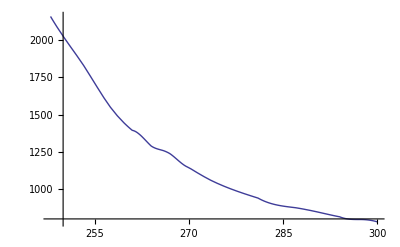

```mathematica
Plot[%71[x],{x,248,300}]
```

```mathematica
f2=Interpolation[data2]
```

InterpolatingFunction[{{600,1048}},<>]

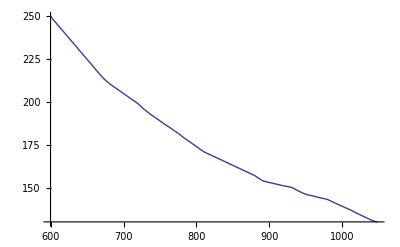

```mathematica
Plot[%72[x],{x,600,1048}]
```

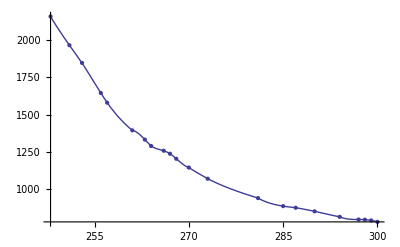

```mathematica
Show[ListPlot[data1],Plot[f1[x],{x,248,300}]]
```

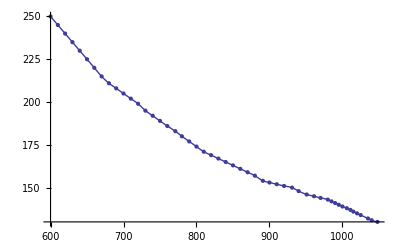

```mathematica
Show[ListPlot[data2],Plot[f2[x],{x,600,1050}]]
```

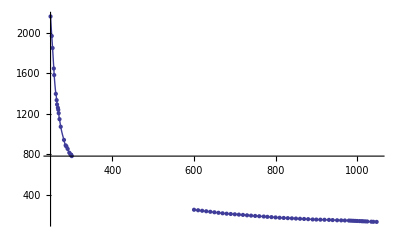

```mathematica
Show[%80,%81,PlotRange->Automatic]
```

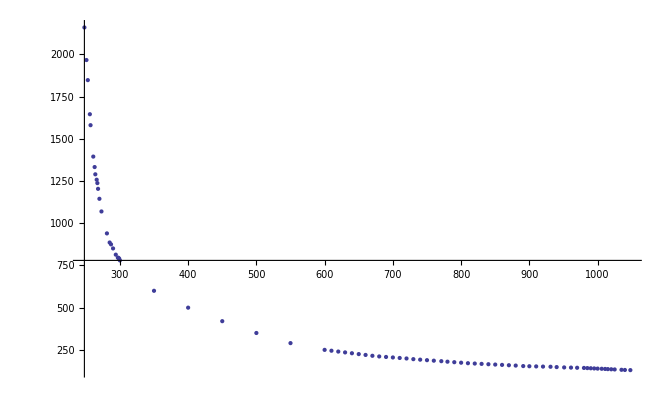

```mathematica
Show[ListPlot[data1],ListPlot[data2],ListPlot[{{350,600},{400,500},{450,420},{500,350},{550,290}}],PlotRange->Automatic]
```